```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/dj/gensim

## Data

```mathematica
(* All data is in the form {vector size, epochs, sparseness value} *)
initialAvgDensityData=Import["src/doc2vec_models/avg_doc_vector_density.txt","Data"];
initialMedianDensityData=Import["src/doc2vec_models/median_doc_vector_density.txt","Data"];
```

```mathematica
(* Data after running multiple simulations to analyze vector density with multiple random initializations *)
(* {vector size, epochs, sparseness value} *)
avgDensityData=Import["models/avg_doc_vector_density.txt","Data"];
medianDensityData=Import["models/median_doc_vector_density.txt","Data"];
```

## Sparseness Measure Visualization

A sparseness value of 0 indicates the vectors were dense and a value of 1 indicates the vectors were sparse.
Sparseness was calculated using s(x)=(√n-(||x(||)_1)/(||x(||)_2))/(√n-1)where  n is the vector size and ||*(||)_1 and ||*(||)_2 are the L_1 and L_2 norms, respectively.

```mathematica
s[x_]:=If[Norm[x,2]==0,1,(√2.-N[Norm[x,1]/Norm[x,2]])/(√2.-1)]
```

```mathematica
ListPlot3D[Flatten[Table[{i,j,s[{i,j}]},{i,-10,10,0.1},{j,-10,10,0.1}],1],AxesLabel->{"x","y","Sparseness Measure"}]
```

-Graphics3D-

## Data Visualization (Initial)

### 3D Plots

```mathematica
ListPointPlot3D[avgDensityData,AxesLabel->{"Vector Size","Epochs","Sparseness Measure"}]
ListPointPlot3D[medianDensityData,AxesLabel->{"Vector Size","Epochs","Sparseness Measure"}]
```

-Graphics3D-

-Graphics3D-

### 2D Plots

```mathematica
showEpochsVsAvgSparseness[vs_]:=ListPlot[{#⟦2⟧,#⟦3⟧}&/@Select[initialAvgDensityData,#⟦1⟧==vs&],AxesLabel->{"Epochs","Avg Sparseness"},PlotLabel->"Vector Size = "<>ToString[vs],Filling->Axis];
showEpochsVsMedianSparseness[vs_]:=ListPlot[{#⟦2⟧,#⟦3⟧}&/@Select[initialMedianDensityData,#⟦1⟧==vs&],AxesLabel->{"Epochs","Median Sparseness"},PlotLabel->"Vector Size = "<>ToString[vs],Filling->Axis];

showVectorSizeVsAvgSparseness[epochs_]:=ListPlot[{#⟦1⟧,#⟦3⟧}&/@Select[initialAvgDensityData,#⟦2⟧==epochs&],AxesLabel->{"Vector Size","Avg Sparseness"},
PlotLabel->"Epochs = "<>ToString[epochs],Filling->Axis,PlotRange->{{5,50},{0.15,0.35}}];
showVectorSizeVsMedianSparseness[epochs_]:=ListPlot[{#⟦1⟧,#⟦3⟧}&/@Select[initialMedianDensityData,#⟦2⟧==epochs&],AxesLabel->{"Vector Size","Median Sparseness"},PlotLabel->"Epochs = "<>ToString[epochs],Filling->Axis,PlotRange->{{5,50},{0.15,0.35}},PlotStyle->Red];
```

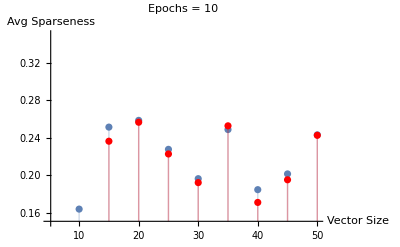
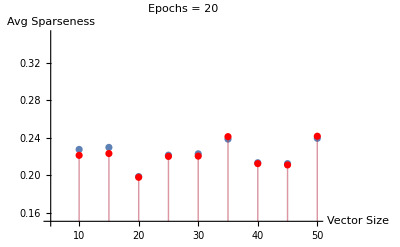
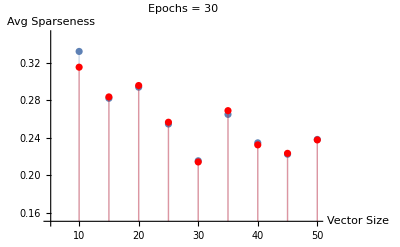
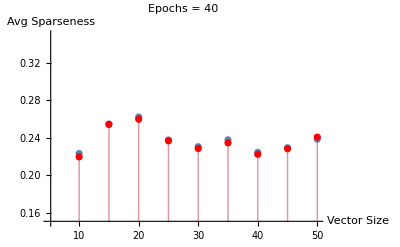
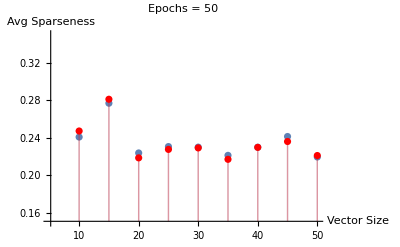
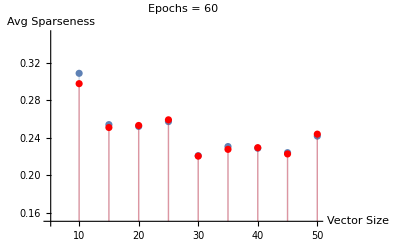
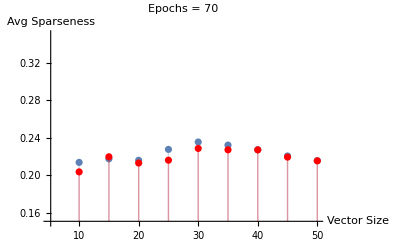
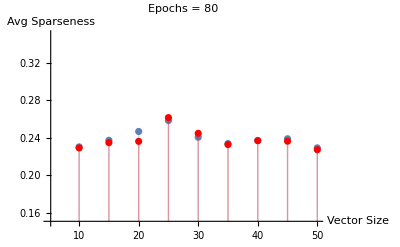

```mathematica
Show[
showVectorSizeVsAvgSparseness[#],
showVectorSizeVsMedianSparseness[#]
]&/@Range[10,100,10]
```

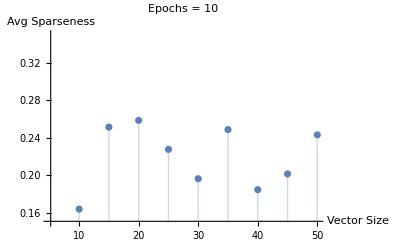
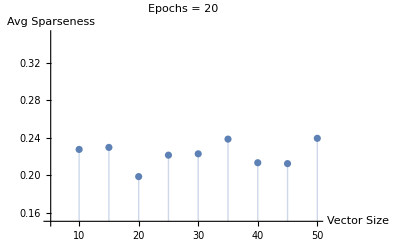
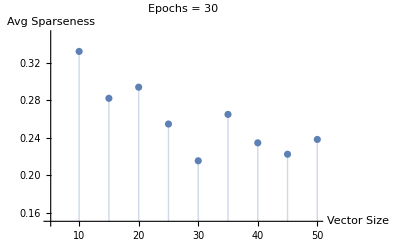
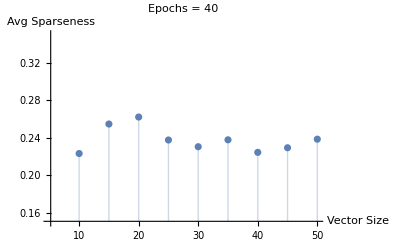
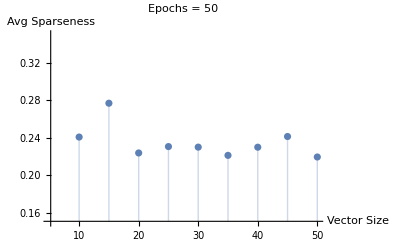
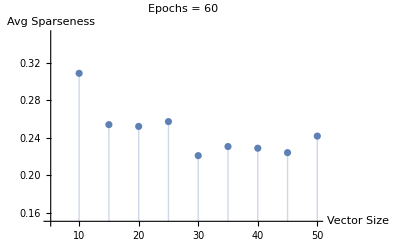
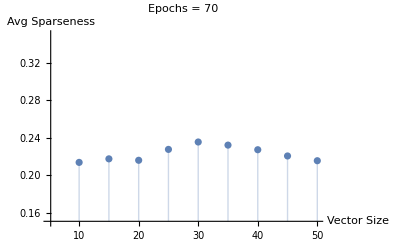
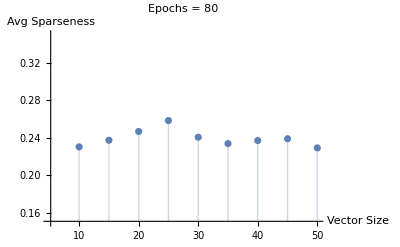

```mathematica
showVectorSizeVsAvgSparseness/@Range[10,100,10]
showVectorSizeVsMedianSparseness/@Range[10,100,10]
```

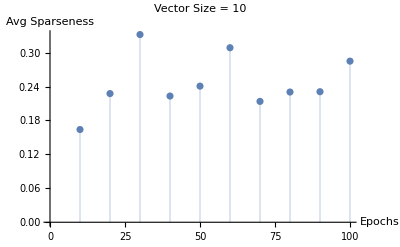
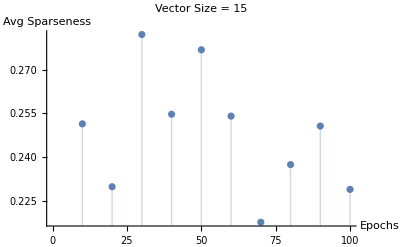
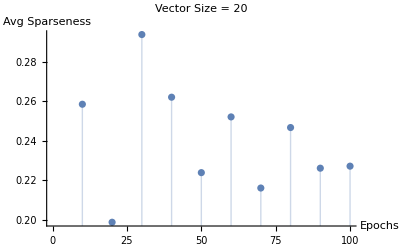
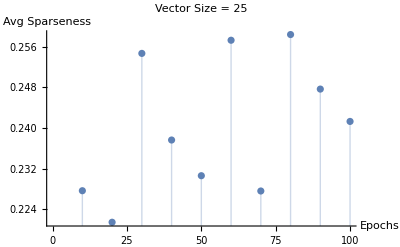
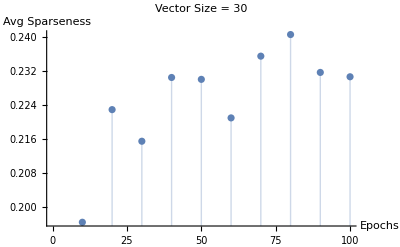
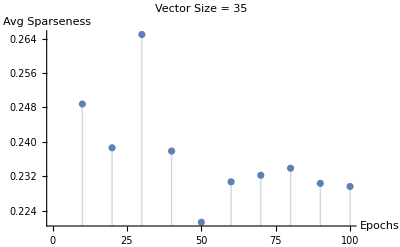
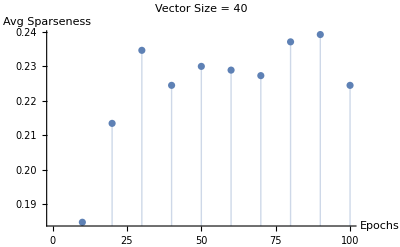
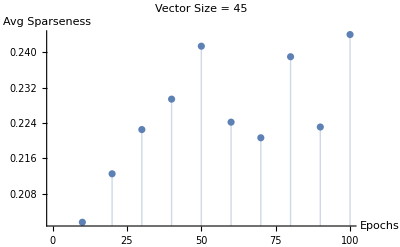

```mathematica
showEpochsVsAvgSparseness/@Range[10,50,5]
showEpochsVsMedianSparseness/@Range[10,50,5]
```

## Data Visualization (Multiple Simulations)

```mathematica
getMultipleSimulationVectorSizeVsAvgSparseness[epochs_]:={#⟦1⟧,#⟦3⟧}&/@Select[avgDensityData,#⟦2⟧==epochs&];
getMultipleSimulationVectorSizeVsMedianSparseness[epochs_]:={#⟦1⟧,#⟦3⟧}&/@Select[medianDensityData,#⟦2⟧==epochs&];
```

```mathematica
showMultipleSimulationVectorSizeVsAvgSparseness[epochs_]:=ListPlot[getMultipleSimulationVectorSizeVsAvgSparseness[epochs],PlotRange->{{5,55},{0.15,0.35}},AxesLabel->{"Vector Size","Avg Sparseness"},PlotLabel->"Epochs = "<>ToString[epochs],ImageSize->Large]
showMultipleSimulationVectorSizeVsMedianSparseness[epochs_]:=ListPlot[getMultipleSimulationVectorSizeVsMedianSparseness[epochs],PlotRange->{{5,55},{0.15,0.35}},AxesLabel->{"Vector Size","Median Sparseness"},PlotLabel->"Epochs = "<>ToString[epochs],ImageSize->Large]
```

```mathematica
showMultipleSimulationVectorSizeVsAvgSparseness/@Range[10,100,10];
```

```mathematica
getAvgSparsenessListVectorSizeAndEpochs[vs_,e_]:=Select[getMultipleSimulationVectorSizeVsAvgSparseness[e],#⟦1⟧==vs&]⟦All,2⟧
showMultipleSimulationBoxWhiskerChartAvgSparseness[epochs_]:=BoxWhiskerChart[getAvgSparsenessListVectorSizeAndEpochs[#,epochs]&/@Range[10,50,10],"Outliers",ChartLabels->{10,20,30,40,50},PlotLabel->"Average Sparseness with Epochs = "<>ToString[epochs],ImageSize->Medium,PlotRange->{0.15,0.4}]

getMedianSparsenessListVectorSizeAndEpochs[vs_,e_]:=Select[getMultipleSimulationVectorSizeVsMedianSparseness[e],#⟦1⟧==vs&]⟦All,2⟧
showMultipleSimulationBoxWhiskerChartMedianSparseness[epochs_]:=BoxWhiskerChart[getMedianSparsenessListVectorSizeAndEpochs[#,epochs]&/@Range[10,50,10],"Outliers",ChartLabels->{10,20,30,40,50},PlotLabel->"Median Sparseness with Epochs = "<>ToString[epochs],ImageSize->Medium,PlotRange->{0.15,0.4}]
```

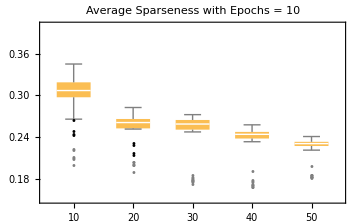
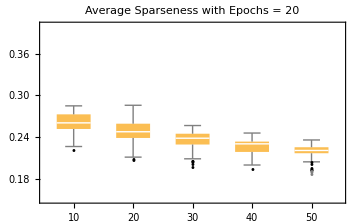
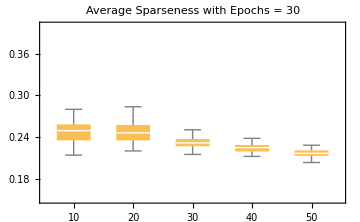
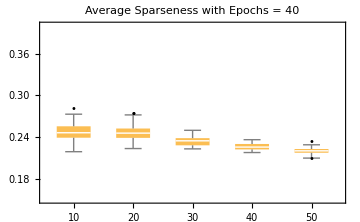
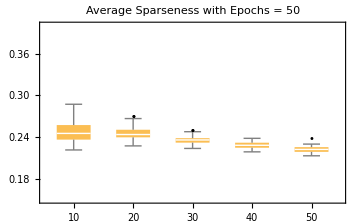
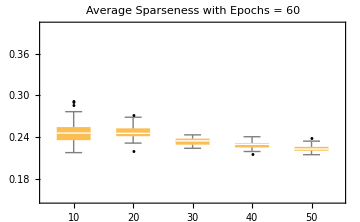
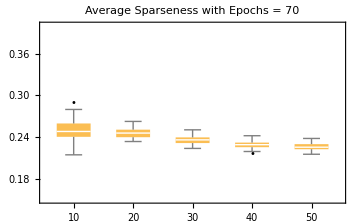
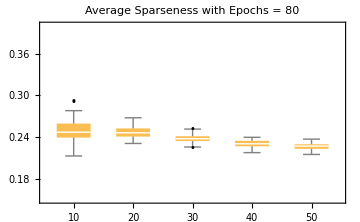

```mathematica
showMultipleSimulationBoxWhiskerChartAvgSparseness/@Range[10,100,10]
```

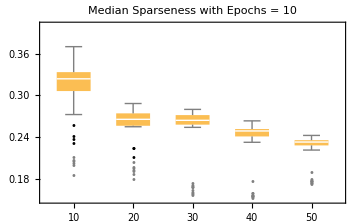
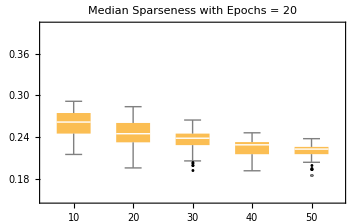
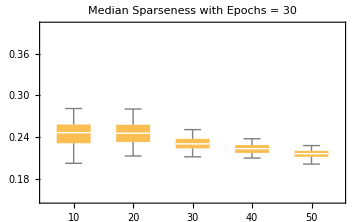
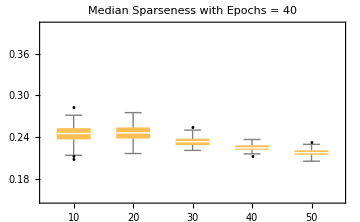
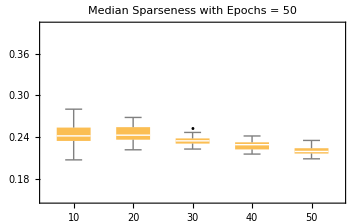
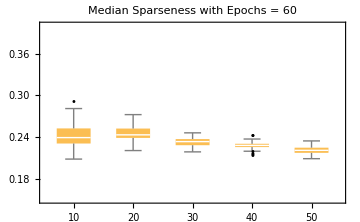
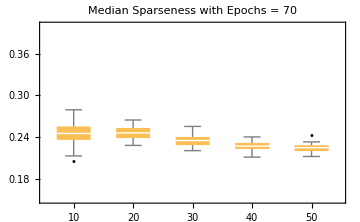
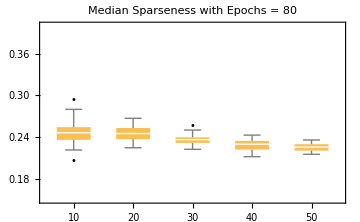

```mathematica
showMultipleSimulationBoxWhiskerChartMedianSparseness/@Range[10,100,10]
```

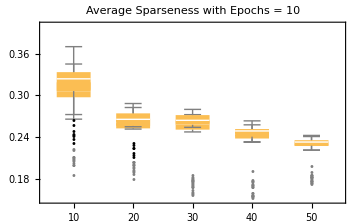
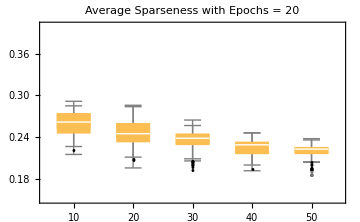
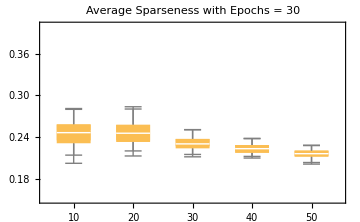
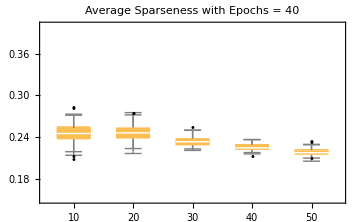
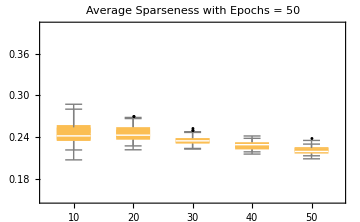
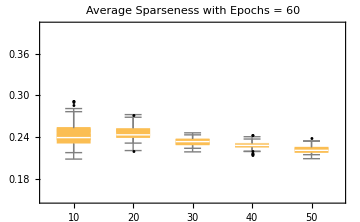
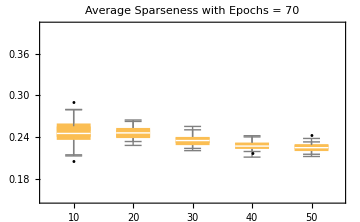
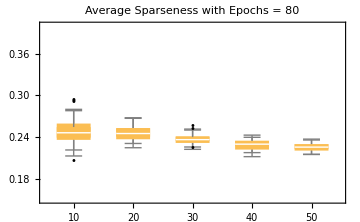

```mathematica
Show[
showMultipleSimulationBoxWhiskerChartAvgSparseness@#,
showMultipleSimulationBoxWhiskerChartMedianSparseness@#
]&/@Range[10,100,10]
```